```mathematica
LT[f_,t_,s_]:=∫_(-∞)^∞ f ⅇ^(-s t)ⅆt (* Bilateral Laplace Defined *)
```

```mathematica
f[t_]:=Exp[-2 Abs[t]]
```

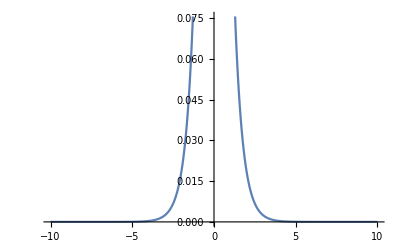

```mathematica
Plot[f[t],{t,-10,10}]
```

```mathematica
F=ConditionalExpression[-4/((-2+s) (2+s)),-2<Re[s]<2]
```

```mathematica
ConditionalExpression[-4/((-2+s) (2+s)),-2<Re[s]<2]
F=(s+10)/(s^2+4s+8)
```

ConditionalExpression[-4/((-2+s) (2+s)),-2<Re[s]<2]

(10+s)/(8+4 s+s^2)

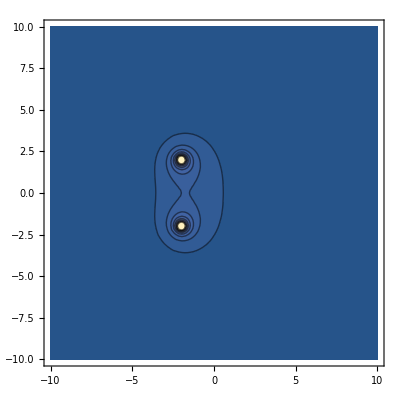
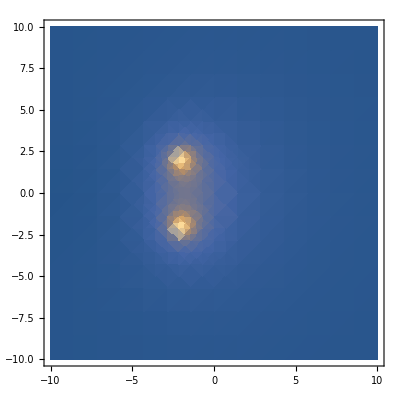
{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
Block[{s=σ+I ω},Table[plot[Abs[F],{σ,-10,10},{ω,-10,10},PlotRange->Full],{plot,{Plot3D,ContourPlot,DensityPlot}}]]
```